# Midterm 1

Note: If you get to a part where you know exactly what you need to do but don’t know how to make Mathematica do it, please write clearly and explicitly what you would do. We will give you at least partial credit for correct reasoning even if the code doesn’t quite work. (But do your best to get the code to work! All Mathematica techniques you will need for this exam you have already seen in some form in the homework.)

```mathematica
Quit[]
```

## Problem 4

Consider a nonlinear spring for which the restoring force is F = -kx^3, where k is a type of spring constant and x is the displacement from the equilibrium length of the spring.

A) (1 point) What are the units of k? Your answer here---> Since x is in units of distance or length (let’s say meters), k needs to be in units of (kg*m^4)/s^2 so that both sides of the equation are in newtons.
B) (1 point) Derive the potential energy associated with this force, assuming U=0 when the spring is at its equilibrium length. Your answer here---> Since F=-Gradient[U] for conservative forces, we can integrate the negative of F for U...U=(1/4)*k*x^4

We now hang a spherical mass of 0.145 kg and diameter 0.075 m from this type of nonlinear spring and set it in motion. The spring constant is 5.0 as expressed in standard units.  We do this on an exoplanet with a thick atmosphere, so the coefficients β and γ as defined in Eq. 2.4 of the textbook have considerably larger values than at STP on Earth. Under the surface conditions of this exoplanet, β = 6.4×10^-2 N s/m^2 and γ = 1.0 N s^2/m^4. By amazing coincidence, the acceleration due to gravity on the surface of this planet is still 9.81 m/s^2.

```mathematica
(* given quantities *)
m=0.145;
d=.075;
k=5;

beta=6.4*10^-2;
gamma=1.0;
g=9.81;
```

C) (1 point) Compute the linear and quadratic drag coefficients.

```mathematica
b=beta*d (* linear drag coefficient *)
c = gamma*d^2 (* quadratic drag coefficient *)
```

0.0048

0.005625

D) (1 point) Calculate the distance ystretch that the spring stretches when the mass hangs stationary from it. (Note that this may be an impressively long spring!)

```mathematica
ystretch = (m*g)/k
```

0.28449

E) (5 points) Using Newton’s 2nd Law, write down the differential equation for y[t], where y is the vertical displacement of the mass on the spring as measured from the unstretched length of the spring. Hint: If you find yourself needing to use the absolute value of a function, you may use the Abs operation in Mathematica. For example, if you want the absolute value of a function f[x], you can do Abs[f[x]].

```mathematica
eqy=m*y''[t]==-(k*(y[t])^3)-(m*g)-(b*y'[t])-((y'[t]*(c*(y'[t])^2))/Abs[y'[t]])
```

0.145 y''[t]==-1.42245-5 y[t]^3-0.0048 y'[t]-(0.005625 y'[t]^3)/Abs[y'[t]]

F) (5 points) The mass is initially at equilibrium hanging from the spring. You then kick the mass sharply upwards, giving it an initial speed of 8 m/s. Solve the differential equation for the first 100 seconds given these initial conditions. Plot the first several seconds of the motion, together with a horizontal line representing the initial y position. Using the plot, determine to the nearest quarter of a second how long it takes for the mass to make 5 complete oscillations.

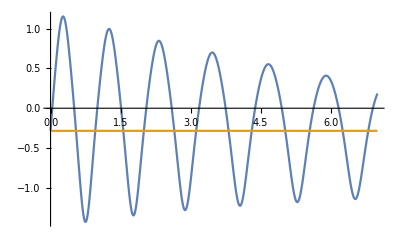

```mathematica
v0=8;
y0=-ystretch;
sol=NDSolve[{eqy,y[0]==y0,y'[0]==8},{y},{t,0,100}];
Plot[{y[t]/.sol,-ystretch},{t,0,7}]
```

Length of time to complete 5 oscillations: 5.55 seconds

G) (2 points) Now plot the solution at significantly later times (80 seconds or later), when the amplitude of oscillations is much smaller. Compared to the early-time oscillations with larger amplitude, has the frequency of oscillations increased, decreased, or remained the same? Is this behavior the same or different from the behavior of an ideal linear spring subject to damping?

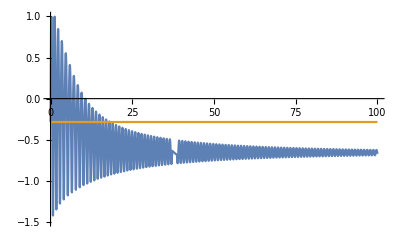

```mathematica
Plot[{y[t]/.sol,-ystretch},{t,0,100},PlotRange->{-1.5,1}]
```

Frequency of oscillations has: increased/decreased/remained the same (choose one)------>remained the same
Compared to linear springs, this behavior is: same/different (choose one)----->same

H) (4 points) Determine the total work done by the combined drag forces after the first 10 seconds of motion have elapsed. Hint: If you want to find the position or velocity at a given time, say 1.5 seconds, you can use y[1.5]/.sol and y’[1.5]/.sol.

```mathematica
v10sec=y'[10]/.sol
p10sec=y[10]/.sol
E10sec=(1/4)*k*p10sec^4+(1/2)*m*v10sec^2
E0=(1/2)*m*v0^2
workNC = E10sec-E0
```

{-2.42756}

{-0.934385}

{1.38007}

4.64

{-3.25993}

Solution : -3.25993 Joules

## Problem 5

Two positive charges of Q = 0.024 C are fixed in place at r1 = (0,0,0) and r2 = (0,0,1) in meters. Another charge of q = 1.15 μC and mass m = 1 kg is located at the position vector r = (x, y, z) and is free to move under the influence of the Coulomb force. Assume no other forces are present. The goal of this problem is to calculate where the particle will be after 1 second given the initial conditions provided later in the problem.

```mathematica
Clear["`*"]
```

```mathematica
k=8.99*10^9;

Q=2.4*10^-2;
r1={0,0,0};
r2={0,0,1};

q=1.15*10^-6;
r={x[t],y[t],z[t]}; (* we use the function notation so we can solve the differential equations later *) 
m=1;
```

(6 points) Calculate the total potential energy of the system in terms of x[t], y[t], and z[t].

```mathematica
U = ((k*Q*Q)/(Norm[r1-r2]))+((k*Q*q)/(Norm[r2-r]))+((k*Q*q)/(Norm[r1-r]))
(* The following line will clean things up a bit. Don't worry about any small imaginary part. *)
U =ComplexExpand[U]
```

5.17824×10^6+248.124/(√(Abs[x[t]]^2+Abs[y[t]]^2+Abs[1-z[t]]^2))+248.124/(√(Abs[x[t]]^2+Abs[y[t]]^2+Abs[z[t]]^2))

(5.17824×10^6+0. ⅈ)+248.124/(√(x[t]^2+y[t]^2+(1-z[t])^2))+248.124/(√(x[t]^2+y[t]^2+z[t]^2))

(6 points) Calculate the force on q.

```mathematica
F=-Grad[U,{x[t],y[t],z[t]}]
```

{(248.124 x[t])/((x[t]^2+y[t]^2+(1-z[t])^2)^(3/2))+(248.124 x[t])/((x[t]^2+y[t]^2+z[t]^2)^(3/2)),(248.124 y[t])/((x[t]^2+y[t]^2+(1-z[t])^2)^(3/2))+(248.124 y[t])/((x[t]^2+y[t]^2+z[t]^2)^(3/2)),-(248.124 (1-z[t]))/((x[t]^2+y[t]^2+(1-z[t])^2)^(3/2))+(248.124 z[t])/((x[t]^2+y[t]^2+z[t]^2)^(3/2))}

(7 points) Write down the equations of motion for the x, y, and z directions using Newton’s 2nd Law. Solve the equations for the following initial conditions: r0 = {3.2, 1.4, 4.0}, v0 = {-15.0, -10.0, -20.0}. Plot the result.

```mathematica
eqx = F[[1]]==m*x''[t];
eqy = F[[2]]==m*y''[t];
eqz = F[[3]]==m*z''[t];

sol1=NDSolve[{eqx,eqy,eqz,x[0]==3.2,y[0]==1.4,z[0]==4.0,x'[0]==-15.0,y'[0]==-10.0,z'[0]==-20.0},{x,y,z},{t,0,1}];
ParametricPlot3D[{x[t],y[t],z[t]}/.sol1,{t,0,1}]
```

-Graphics3D-

(1 point) Determine the position of q after 1 second.

```mathematica
{x[1],y[1],z[1]}/.sol1
```

{{15.0456,-14.417,-9.52571}}